## Discrete example

```mathematica
vPrior = {3/4,1/4};
vLikelihood = {1/10,4/5};
vNumerator = vPrior*vLikelihood;
vPosterior = (vPrior*vLikelihood)/Total[vPrior*vLikelihood];
```

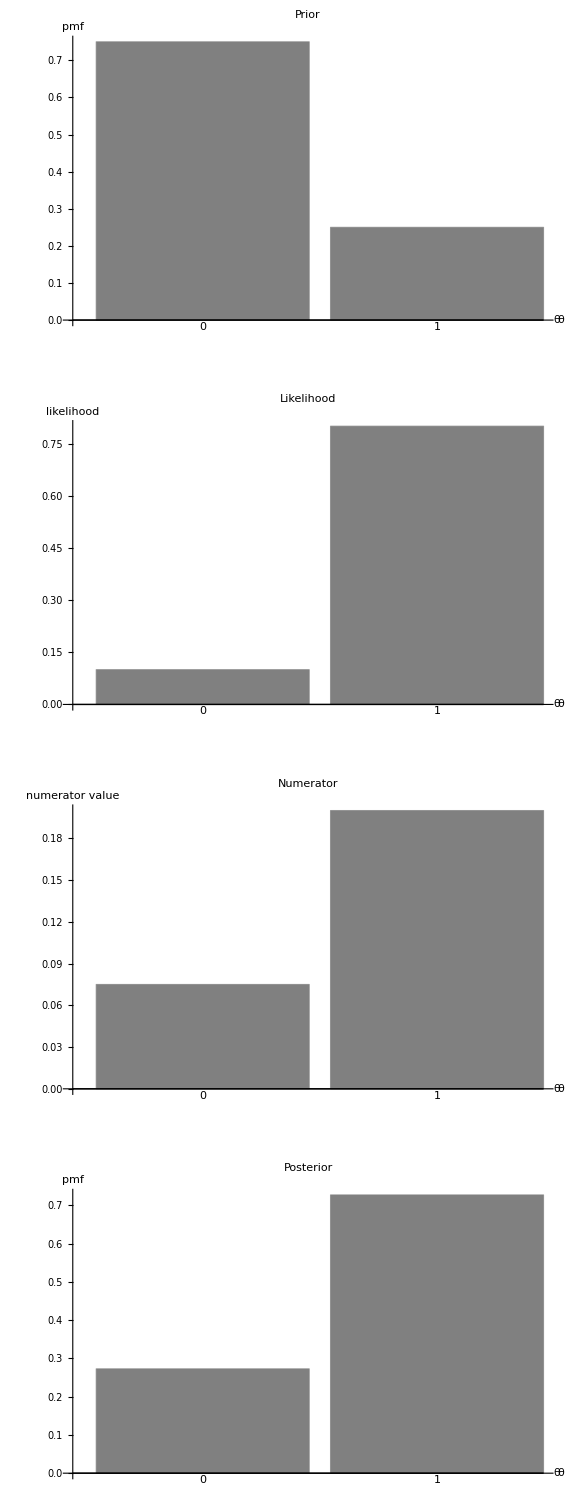

```mathematica
g1=BarChart[vPrior,ChartLabels->{0,1},ChartStyle->{Gray},BaseStyle->{FontSize->16},AxesLabel->{θ,"pmf"},PlotLabel->"Prior"];
g2 = BarChart[vLikelihood,ChartLabels->{0,1},ChartStyle->{Gray},BaseStyle->{FontSize->16},AxesLabel->{θ,"likelihood"},PlotLabel->"Likelihood"];
g3 = BarChart[vNumerator,ChartLabels->{0,1},ChartStyle->{Gray},BaseStyle->{FontSize->16},AxesLabel->{θ,"numerator value"},PlotLabel->"Numerator"];
g4 = BarChart[vPosterior,ChartLabels->{0,1},ChartStyle->{Gray},BaseStyle->{FontSize->16},AxesLabel->{θ,"pmf"},PlotLabel->"Posterior"];
Show[GraphicsColumn[{g1,g2,g3,g4}],ImageSize->Large]
```

```mathematica
?ImageSize
```

ImageSize is an option that specifies the overall size of an image to display for an object.